#### Matching-based Capture Strategies for 3D heterogeneous multiplayer reach-avoid differential games by Rui Yan, Xiaoming Duan, Zongying Shi, Yisheng Zhong, Francesco Bullo. Automatica. 21 January, 2021.

```mathematica
RemoveAbs[x_]:=FullSimplify[ComplexExpand[Sqrt[x Conjugate[x]]]]
```

```mathematica
Function[x,FullSimplify[ComplexExpand[√(x Conjugate[x])]]]
```

Function[x,FullSimplify[ComplexExpand[√(x Conjugate[x])]]]

```mathematica
Function[x,FullSimplify[ComplexExpand[√(x Conjugate[x])]]]
```

Function[x,FullSimplify[ComplexExpand[√(x Conjugate[x])]]]

#### Potential Function -- Equation (3)

```mathematica
f[_,_, _, _] = ComplexExpand[Norm[{-}]-* Norm[{-}]-]
```

-r_i+√((x-x_p)^2)-√((x-x_e)^2) α_(i j)

#### Gradient of the Potential Function w.r.t

```mathematica
FullSimplify[D[-Subscript[r, i]+√((x-xp)^2)-√((x-xe)^2) Subscript[α, i j], x]]
```

(x-xp)/(√((x-xp)^2))+((-x+xe) α_(i j))/(√((x-xe)^2))

Proof of Lemma 3.1: (Evasion Space for One Pursuer). For the ES \mathbb{E} with respect to   \in \mathcal{P}  and E_j \in \mathcal{E} its closure is bounded and strictly convex.

```mathematica
Eq5[_, e_, _] = ComplexExpand[Norm[{xej+ *e-xpi}]- -ri]
```

Set::write: Tag Integer in 0[ρ _,e_,_ α_(i j)] is Protected.

-ri+√((xej-xpi+e ρ)^2)-α_(i j)

```mathematica
H[x1_, x2_,x3_, x4_, x5_, x6_, x7_, x8_] = (2*x1*x3)/(sqrt[x1^2 + x5^2])+(2*x2*x4)/(sqrt[x2^2 + x6^2])+(2*x5*x7)/(sqrt[x1^2 + x5^2])+(2*x6*x8)/(sqrt[x2^2 + x6^2])
```

(2 x1 x3)/sqrt[x1^2+x5^2]+(2 x5 x7)/sqrt[x1^2+x5^2]+(2 x2 x4)/sqrt[x2^2+x6^2]+(2 x6 x8)/sqrt[x2^2+x6^2]

```mathematica
D[H[x1, x2,x3, x4, x5, x6, x7, x8], x3]
```

(2 x1)/sqrt[x1^2+x5^2]

```mathematica
With[{x3=a*Sin[u]},D[H[x1, x2,x3, x4, x5, x6, x7, x8], x3]]
```

General::ivar: a Sin[u] is not a valid variable.

∂_(a Sin[u]) ((2 x5 x7)/sqrt[x1^2+x5^2]+(2 a x1 Sin[u])/sqrt[x1^2+x5^2]+(2 x2 x4)/sqrt[x2^2+x6^2]+(2 x6 x8)/sqrt[x2^2+x6^2])

```mathematica
D[H[x1, x2,x3, x4, x5, x6, x7, x8], x3]-> (x3= Integrate[a*Sin[u]])
```

```mathematica
x3[u_] = Integrate[a*Cos[u], u]
```

a Sin[u]

```mathematica
Vx[x1_, x2_,x3_, x4_] = 2*x1*x3/(Sqrt[x1^2+x2^2])+2*x2*x4/(Sqrt[x1^2+x2^2])
```

(2 x1 x3)/(√(x1^2+x2^2))+(2 x2 x4)/(√(x1^2+x2^2))

```mathematica
FullSimplify[D[Vx[x1, x2,x3, x4], x1]+D[Vx[x1, x2,x3, x4], x2]+D[Vx[x1, x2,x3, x4], x3]+D[Vx[x1, x2,x3, x4], x4]]
```

(2 (x1^3+x2^2 (x2+x3)+x1 x2 (x2-x3-x4)+x1^2 (x2+x4)))/((x1^2+x2^2)^(3/2))

```mathematica
Simplify[(2 (x1^3+x2^2 (x2+x3)+x1 x2 (x2-x3-x4)+x1^2 (x2+x4)))/((x1^2+x2^2)^(3/2))]
```

(2 (x1^3+x2^2 (x2+x3)+x1 x2 (x2-x3-x4)+x1^2 (x2+x4)))/((x1^2+x2^2)^(3/2))

```mathematica
v = Exp[∫Bⅆs ]
```

ⅇ^(B s)

```mathematica
Plot3D[v,{B,-11.885010282371429,11.881936950584315},{s,-11.884987975537284,11.881959250332164}]
```

-Graphics3D-

```mathematica
D[Exp[∫Bⅆs ]]
```

ⅇ^(B s)

```mathematica
D[Exp[∫x ⅆx]]
```

ⅇ^(x^2/2)

```mathematica
Plot[ⅇ^(x^2/2),{x,-14.696938456699069,14.696938456699069}]
```

-Graphics-

```mathematica
∫Exp[x]ⅆx
```

ⅇ^x

```mathematica
D[∫Exp[x]ⅆx]
```

ⅇ^x

```mathematica
D[Exp[x]]
```

ⅇ^x

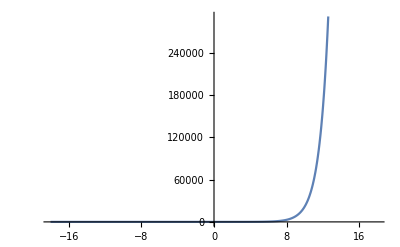

```mathematica
Plot[ⅇ^x,{x,-18.,18.}]
```